# Electromagnetic Optics

-Graphics-

```mathematica
ew[t_,τ_, f_ ] := Exp[-t^2/τ^2] Exp[I 2 π f t];
```

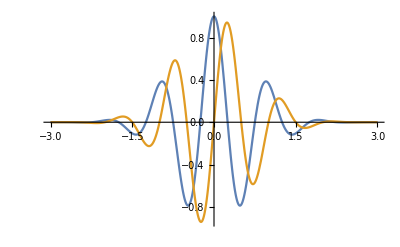

```mathematica
τ=1; f=1;
Plot[{Re[ew[t, τ, f]], Im[ew[t, τ, f]]}, {t, -3/f, 3/f}, PlotRange->Full]
```

```mathematica
Ev= {ew[t-z/c, τ, f], 0,0}
Bv=FullSimplify[Integrate[-Curl[Ev, {x, y, z}], t]]
```

{ⅇ^(2 ⅈ π (t-z/c)-(t-z/c)^2),0,0}

{0,(ⅇ^(((c t-z) (2 ⅈ c π-c t+z))/c^2))/c,0}

```mathematica
Manipulate[Show[ParametricPlot3D[ {With[{t=t, c=1}, Re[Evaluate[Ev]]]+{0,0,z}, With[{t=t,c=1}, Re[Evaluate[Bv]]]+{0,0,z}},{z,-2,5}, PlotRange->{-1.5,1.5}],Graphics3D[{Red,Arrowheads[0.01],Arrow[{{0,0,0},{Re[With[{t=t, c=1, z=0}, Evaluate[Ev ]]][[1]],0,0}}],
Blue, Arrow[{{0,0,0}, {0,Re[With[{t=t, c=1, z=0}, Evaluate[Bv ]]][[2]],0}}]}]], {t, -1, 2.5}]
```

```mathematica
Graphics3D[{Red,Arrow[{{0,0,0},{1,1,1}}],
Blue, Arrow[{{2,0,1}, {1,1,1}}]}]
```

-Graphics3D-